# Figure 1

```mathematica
R=50; (*quibit frequency*)
g=1/2^(1/2); (*coupling*)
γ=0.5;(*Stark*)
H[q_,p_]=(q^2+p^2)/2-(1/2)*(1+(Sqrt[2]*g*q)^2)^(1/2);
V[q_,gg_]=q^2/2-(1/2)*(1+(Sqrt[2]*gg*q)^2)^(1/2);
```

#### First column

```mathematica
(*Necessary to check the energy of the degenerated minima and the local maximum*)
```

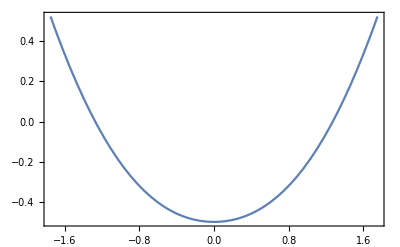

```mathematica
pot=Show[Plot[V[q,g],{q,-1.75,1.75},Frame->True,Axes->False,LabelStyle->{Black,15}],Plot[{},{x,-1.75,1.75},PlotStyle->{{Dashed,Gray}}]]
```

#### Second column

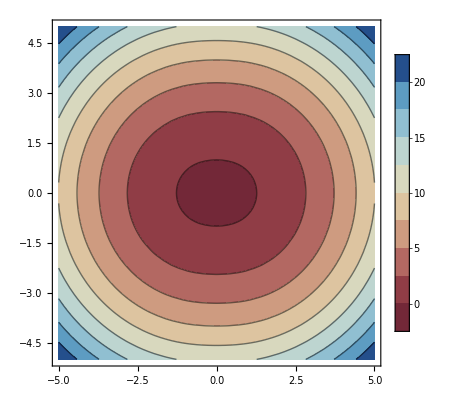

```mathematica
contour=ContourPlot[H[q,p],{q,-5,5},{p,-5,5},PlotLegends->Automatic,LabelStyle->{22,Black},ColorFunction->"RedBlueTones"]
```